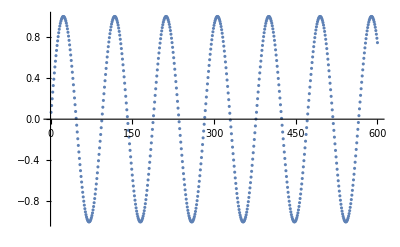

{-6.15752,12.336,18.5145,24.7558,31.1227,37.6782,39.9192}

```mathematica
FindMax[list_]:=Position[list,Max@list][[1,1]];
FD[]:=First/@(Take[#,Round[(Length@#)/2.]]&@FindPeaks@Abs@Fourier@Data);
HDFD[index_]:=Abs@Fourier[Data*Exp[2I π(index-2)N@(Range@Len-1)/Len],FourierParameters->{0,2/Len}];

CollectIndices[i_]:=(#-2+2(FindMax@HDFD@#-1)/Len)&/@i;

FindIndexFreq[i_]:=N@(CollectIndices[i]*2π*Rate/Len);

RecoverFreqList[]:=(Select[FD[],#>0&]//FindIndexFreq);
RecoverDataFreq[i_]:=If[i≤Length@#,#[[i]],#[[Length@#]]]&@RecoverFreqList[];

Len=600;
Rate=600;
Time=N@Range@Len/Rate;

Freq=40;

Data=Sin[Freq*Time];
ListPlot[Data]

FindIndexFreq[Range@7]
```